```mathematica
布朗粒子的能量统计
```

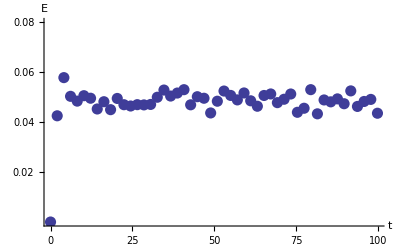

```mathematica
dis=NormalDistribution[0,1];
n=500;α=0.7;
m=1000;δt=0.1;time=(m-1)*δt;
fr=Table[RandomReal[dis] √α,{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{x''[t]+α*x'[t]==fr[[i]][t],
x[0]==0,x'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],x,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[
section=Table[x'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[section[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->{0,0.08},AxesLabel->{"t","E"},
Ticks->{Automatic,0.02Range[4]},
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[dis,α,equ,fr,s,sample,result,x]
```